# QKT Classic

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2025\PAPER III chaotic phase space\Breaking time reversal symmetries

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[change];
change[s_]:=Module[{B=Sqrt[2/(1-s[[3]])]},
{s[[1]]*B,s[[2]]*B}
];
Clear[change2];
change2[Q_]:=Module[{B=Norm[Q]},
{Q[[1]]*Sqrt[1-(1/4)B^2],Q[[2]]*Sqrt[1-(1/4)B^2],(1/2)B^2 -1}
];

Clear[F,Fun];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
Clear[mapeo];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];
mapeob[Qini_,α_,k_,n_]:=Module[{map={},snew,a,s,Qnew},
AppendTo[map,Qini];
s=change2[Qini];
Do[
snew=MatrixPower[N[F[α,k,s]],2].s;
AppendTo[map,change[snew]];
s=snew;
,{l,1,n}];
map
];

Clear[Jx,Jy,Jz,M,mapeo1,jmas];
Jx[x_,y_,z_,α_,k_]:=x*Cos[α]-y*Sin[α]*Cos[k*x]+z*Sin[α]*Sin[k*x];
Jy[x_,y_,z_,α_,k_]:=x*Sin[α]+y*Cos[α]*Cos[k*x]-z*Cos[α]*Sin[k*x];
Jz[x_,y_,z_,α_,k_]:=y*Sin[k*x]+z*Cos[k*x];

M[Jini_,α_Real,k_Real]:=Module[{M},
M={{D[Jx[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jx[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},
{D[Jy[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jy[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}},{D[Jz[x,y,z,α,k], x]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], y]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]},D[Jz[x,y,z,α,k], z]/.{x->Jini[[1]],y->Jini[[2]],z->Jini[[3]]}}}//N;
M
];

mapeo1[si_,α_,k_,n_]:=Module[{s=si},
MatrixPower[F[α,k,s],n].s
];
```

## New mappings

```mathematica
Clear[F,Fun,mapeo];
F[α_,k_,s_]:=Module[{a,sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}
];
Fun[α_,k_,s_]:=Module[{sx=s[[1]]},
{{Cos[α],-Sin[α]Cos[k*sx],Sin[α]Sin[k*sx]},{Sin[α],Cos[α]Cos[k*sx], -Cos[α]Sin[k*sx]},{0,Sin[k*sx],Cos[k*sx]}}.s
];
mapeo[Qini_,α_,k_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun[α,k,#]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[Rxx,Ry,Rz];
Rz[a_]:=Module[{d},
{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}
];
Ry[b_]:=Module[{d},
{{Cos[b],0,Sin[b]},{0,1,0},{-Sin[b],0,Cos[b]}}
];
Rxx[c_,s_]:=Module[{sx=s[[1]]},
{{1,0,0},{0,Cos[c*sx],-Sin[c*sx]},{0,Sin[c*sx],Cos[c*sx]}}
];
```

```mathematica
Clear[Fun2,mapeo2];
Fun2[a_,c_,s_]:=Module[{sx=s[[1]]},
Rz[a].Rxx[c,s].s
];
mapeo2[Qini_,a_,c_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun2[a,c,#]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
ini=change[RandomPoint[Sphere[]]]
```

{0.688839,1.26291}

```mathematica
Clear[a,b,c];
a=0.84;
c=20.0;
```

```mathematica
Fun[a,c,change2[ini]]
```

{0.962003,-0.219636,-0.162206}

```mathematica
Fun2[a,c,change2[ini]]
```

{0.962003,-0.219636,-0.162206}

```mathematica
mapeo[ini,a,c,10]
```

{{0.688839,1.26291},{1.26197,-0.288122},{0.95161,0.791985},{1.59354,0.810383},{1.58458,0.166962},{1.05169,1.21179},{-0.202841,1.5872},{0.336318,-0.472211},{0.464887,0.0277746},{0.25428,1.89992},{1.45573,-1.07576}}

```mathematica
mapeo2[ini,a,c,10]
```

{{0.688839,1.26291},{1.26197,-0.288122},{0.95161,0.791985},{1.59354,0.810383},{1.58458,0.166962},{1.05169,1.21179},{-0.202841,1.5872},{0.336318,-0.472211},{0.464887,0.0277746},{0.25428,1.89992},{1.45573,-1.07576}}

```mathematica
Clear[Fun3,mapeo3];
Fun3[a_,b_,c_,s_]:=Module[{sx=s[[1]]},
Ry[b].Rz[a].Rxx[c,s].s
];
mapeo3[Qini_,a_,b_,c_,n_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun3[a,b,c,#]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
Clear[a,b,c];
c=20.0;
b=1.5;
a=0.84;
```

```mathematica
randomregion=RandomPoint[Disk[{0,0},1.999],300];
```

```mathematica
kicks=2000;
poincare=ParallelTable[mapeo3[i,a,b,c,kicks],{i,randomregion}];
```

```mathematica
poincareplot=ListPlot[Flatten[poincare,1],PlotStyle->Directive[Black,PointSize[0.0015]],PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["(a,b,c) = "<>ToString[N[{a,b,c}]],Black,30]]
```

## Symmetry lines

```mathematica
Clear[rot];
rot[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
```

```mathematica
sym=Table[{i,0},{i,-1.999,1.999,0.005}];
a=0.84;
θ=a/2;
sym=(rot[θ].#&/@sym);
sym//Length
```

800

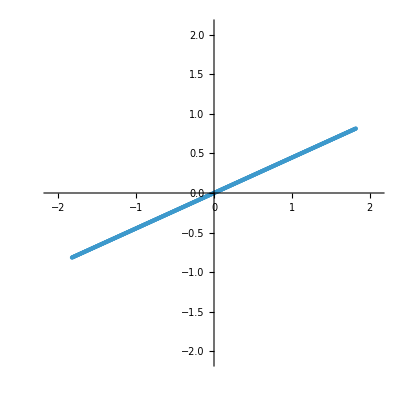

```mathematica
ListPlot[sym,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
kicks=10;
sympoincare=ParallelTable[mapeo3[i,a,b,c,kicks],{i,sym}];
```

```mathematica
symplot=ListPlot[sympoincare,PlotStyle->Directive[PointSize[0.0015]],PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["(a,b,c) = "<>ToString[N[{a,b,c}]],Black,30]]
```

## Powers of Poincaré

```mathematica
Clear[Fun3,mapeo3];
Fun3[a_,b_,c_,s_,p_]:=Module[{sx=s[[1]]},
MatrixPower[Ry[b].Rz[a].Rxx[c,s],p].s
];
mapeo3[Qini_,a_,b_,c_,n_,p_]:=Module[{list,s={Qini[[1]]*Sqrt[1-(1/4)Norm[Qini]^2],Qini[[2]]*Sqrt[1-(1/4)Norm[Qini]^2],(1/2)Norm[Qini]^2 -1}},
list=NestList[Fun3[a,b,c,#,p]&,s,n];
Map[change[#]&,list]
];
```

```mathematica
radius=1.99999;
delta=0.05;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
circlePoints=Select[gridPoints,Norm[#]<radius&];
randomregion=circlePoints;
randomregion//Length
```

5015

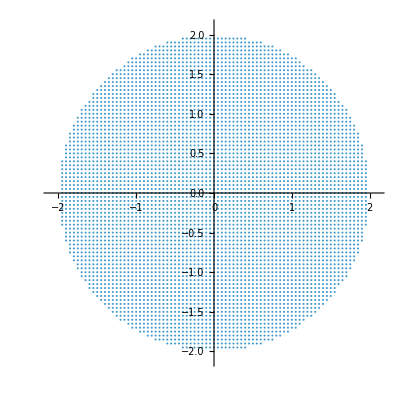

```mathematica
ListPlot[randomregion,AspectRatio->1,PlotRange->{{-2.1,2.1},{-2.1,2.1}}]
```

```mathematica
plist={1,2,100,1000};
kicks=1000;
```

```mathematica
b
```

0.001

```mathematica
Pi/2.
```

1.5708

```mathematica
b=1.8;
p=2000;
puntosa=ParallelTable[Quiet[mapeo3[i,a,b,c,kicks,p]],{i,randomregion},DistributedContexts->Full];
newpoincarea=Flatten[puntosa,1];poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.02],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_c_"<>ToString[N[b]]<>"_c_"<>ToString[c]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>".png",poincarec];
```

```mathematica
Do[
Do[

puntosa=ParallelTable[Quiet[mapeo3[i,a,b,c,kicks,p]],{i,randomregion},DistributedContexts->Full];
newpoincarea=Flatten[puntosa,1];poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.02],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Row[{Style["α = ",45,Black],Style[α*τ,45,Black],Style[", k = ",45,Black], Style[k,50,Black],Style[", n = ",45,Black],Style[kicks,50,Black],Style[", p = ",45,Black],Style[p,50,Black]}],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_b_"<>ToString[N[b]]<>"_c_"<>ToString[c]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>".png",poincarec];

,{p,plist}];
,{b,blist}];
```

$Aborted

# QKT Quantum

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\INVESTIGACION\2025\PAPER III chaotic phase space\Breaking time reversal symmetries

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
Clear[husimi];
husimi[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohes[[i]]].ψ]^2},{i,Length[region]}];
```

```mathematica
radius=1.99999;
delta=0.03;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

14153

```mathematica
ListPlot[region,AspectRatio->1];
```

```mathematica
Clear[J];
J=800;
```

```mathematica
cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region},DistributedContexts->Full];
```

```mathematica
Clear[Floqa];
Floqa[J_,a_,b_,c_]:=N[MatrixExp[(-I*c/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*a)(Sz[J])].MatrixExp[(-I*b)(Sy[J])]];
```

```mathematica
b
```

1.

```mathematica
mat=Floqa[J,a,b,c];
{eigenval,eigenvec}=Eigensystem[mat];
d2=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,cohes},DistributedContexts->Full];
newd2=Transpose[{region[[All,1]],region[[All,2]],-Log[d2]/Log[2J+1]}];
d2plotn=ListDensityPlot[newd2,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", (a,b,c) = "<>ToString[N[{a,b,c}]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
poincare=ParallelTable[mapeo3[i,a,b,c,kicks],{i,randomregion},DistributedContexts->Full];poincareplot=ListPlot[Flatten[poincare,1],PlotStyle->Directive[Gray,Opacity[0.4],PointSize[0.0015]],PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["(a,b,c) = "<>ToString[N[{a,b,c}]],Black,30]];
Export["d2poincare_J_"<>ToString[J]<>"_a_"<>ToString[a]<>"_b_"<>ToString[b]<>"_c_"<>ToString[c]<>"_.png",Show[d2plotn,poincareplot],ImageResolution->300];
```

```mathematica
d2plotn=ListDensityPlot[newd2,PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", (a,b,c) = "<>ToString[N[{a,b,c}]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
poincare=ParallelTable[mapeo3[i,a,b,c,kicks],{i,randomregion},DistributedContexts->Full];poincareplot=ListPlot[Flatten[poincare,1],PlotStyle->Directive[Gray,Opacity[0.4],PointSize[0.0015]],PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["(a,b,c) = "<>ToString[N[{a,b,c}]],Black,30]];
Export["d2poincare_b_J_"<>ToString[J]<>"_a_"<>ToString[a]<>"_b_"<>ToString[b]<>"_c_"<>ToString[c]<>"_.png",Show[d2plotn,poincareplot],ImageResolution->300];
```

```mathematica
blist=N[Range[0,Pi,Pi/20]];
```

```mathematica
p=3000;
```

```mathematica
Do[

mat=Floqa[J,a,b,c];
{eigenval,eigenvec}=Eigensystem[mat];
d2=ParallelTable[Total[Abs[Conjugate[eigenvec].i]^4],{i,cohes},DistributedContexts->Full];
newd2=Transpose[{region[[All,1]],region[[All,2]],-Log[d2]/Log[2J+1]}];
d2plotn=ListDensityPlot[newd2,PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", (a,b,c) = "<>ToString[N[{a,b,c}]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True];
poincare=ParallelTable[mapeo3[i,a,b,c,kicks],{i,randomregion},DistributedContexts->Full];poincareplot=ListPlot[Flatten[poincare,1],PlotStyle->Directive[Gray,Opacity[0.4],PointSize[0.0015]],PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",ImageSize->800,PlotLabel->Style["(a,b,c) = "<>ToString[N[{a,b,c}]],Black,30]];
Export["d2poincare_J_"<>ToString[J]<>"_a_"<>ToString[a]<>"_b_"<>ToString[b]<>"_c_"<>ToString[c]<>"_.png",Show[d2plotn,poincareplot],ImageResolution->300];

puntosa=ParallelTable[Quiet[mapeo3[i,a,b,c,kicks,p]],{i,randomregion},DistributedContexts->Full];
newpoincarea=Flatten[puntosa,1];poincarec=Graphics[{PointSize[0.0025],Blue,Opacity[0.02],Point[newpoincarea]},PlotRange->{{-2.1,2.1},{-2.1,2.1}},AspectRatio->1,PlotLabel->Style["Poincare power 1, (a,b,c) = "<>ToString[N[{a,b,c}]],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,GridLines->Automatic,ImageSize->1000];
Export["poincare_power1_"<>ToString[N[b]]<>"_c_"<>ToString[c]<>"_kicks_"<>ToString[kicks]<>"_p_"<>ToString[p]<>".png",poincarec];

,{b,blist}];
```